# Relaciones de Kramers Kronig

```mathematica
(*En este código se definen las funciones para obtener la parte real o la parte imaginaria del índice de refracción empleando las relaciones de Kramers-Kronig. Además, se añade una función para estimar de manera autoconsistente las partes reales e imaginarias del índice de refracción*)
```

```mathematica
(*La siguiente función calcula la parte imaginaria del índice de refracción k a partir de la parte real n, usando la relación KK*)
(*Entradas: tienen que ser listas de puntos
  omega-vector de frecuencias (debe estar equiespaciado)
nreal-vector de la parte real del índice de refracción
 Salida:
  kimag-vector estimado de la parte imaginaria del índice de refracción*)
```

```mathematica
kkimrefractiveindex[omega_,nreal_]:=Module[{g=Length[omega],
									kimag = ConstantArray[0,Length[nreal]],
									(*a y b son vectores para acumular los puntos*)
									a=ConstantArray[0,Length[nreal]], 
									b=ConstantArray[0,Length[nreal]],
									deltaomega=omega[[2]]-omega[[1]],k,j},
									(*Asegurarse de que sean vectores fila*)
									If[MatrixQ[omega]&&Dimensions[omega][[1]]>Dimensions[omega][[2]],   omega=Transpose[omega]];
									(*Primer punto, excluye omega[[1]]*)

									For[k=2,k<=g,k++,b[[1]] =b[[1]]  + (nreal[[k]]-1) / (omega[[k]]^2 - omega[[1]]^2)];
									kimag[[1]]=-2*omega[[1]]/Pi*deltaomega*b[[1]];
									(*último punto, excluye omega[[g]]*)

									For[k=1,k<=g-1,k++,a[[g]] =a[[g]]  + (nreal[[k]]-1) / (omega[[k]]^2 - omega[[g]]^2)];
									kimag[[g]]=-2*(omega[[g]]/Pi)*(deltaomega*a[[g]]);
									(*Puntos intermedios*)
									For[j=2,j<=g-1,j++,
									For[k=1,k<=j-1,k++,a[[j]] =a[[j]]  + (nreal[[k]]-1) / (omega[[k]]^2 - omega[[j]]^2)];
									For[k=j+1,k<=g,k++,b[[j]] =b[[j]]  + (nreal[[k]]-1) / (omega[[k]]^2 - omega[[j]]^2)];
									kimag[[j]]=-2*omega[[j]]/Pi*deltaomega*(a[[j]]+b[[j]])];
									kimag]
```

```mathematica
(*La siguiente función calcula la parte real del índice de refracción n a partir de la parte imaginaria k, usando la relación KK*)
(*Entradas: tienen que ser listas de puntos
  omega-vector de frecuencias (debe estar equiespaciado)
kimag-vector de la parte imaginaria del índice de refracción
 Salida:
  nreal-vector estimado de la parte real del índice de refracción*)
```

```mathematica
kkrerefractiveindex[omega_,kimag_]:=Module[{g=Length[omega],
									nreal = ConstantArray[0,Length[kimag]],
									(*a y b son vectores para acumular los puntos*)
									a=ConstantArray[0,Length[kimag]], 
									b=ConstantArray[0,Length[kimag]],
									deltaomega=omega[[2]]-omega[[1]],k,j},
									(*Asegurarse de que sean vectores fila*)
									If[MatrixQ[omega]&&Dimensions[omega][[1]]>Dimensions[omega][[2]],   omega=Transpose[omega]];
									(*Primer punto, excluye omega[[1]]*)

									For[k=2,k<=g,k++,b[[1]] =b[[1]]  + (kimag[[k]]*omega[[k]]) / (omega[[k]]^2 - omega[[1]]^2)];
									nreal[[1]]=(2/Pi*deltaomega*b[[1]])+1;
									(*último punto, excluye omega[[g]]*)

									For[k=1,k<=g-1,k++,a[[g]] =a[[g]]  + (kimag[[k]]*omega[[k]]) / (omega[[k]]^2 - omega[[g]]^2)];
									nreal[[g]]=(2/Pi*(deltaomega*a[[g]]))+1;
									(*Puntos intermedios*)
									For[j=2,j<=g-1,j++,
									For[k=1,k<=j-1,k++,a[[j]] =a[[j]]  + (kimag[[k]]*omega[[k]]) / (omega[[k]]^2 - omega[[j]]^2)];
									For[k=j+1,k<=g,k++,b[[j]] =b[[j]]  + (kimag[[k]]*omega[[k]]) / (omega[[k]]^2 - omega[[j]]^2)];
									nreal[[j]]=(2/Pi*deltaomega*(a[[j]]+b[[j]]))+1];
									nreal]
```

```mathematica
(*La siguiente función hace una estimación auto-consistente del índice de refracción complejo utilizando las relaciones de Kramers-Kronig.
Entradas:
omega-vector de frecuencias
reN-vector de la parte real inicial (estimación o medida)
	imN-vector de la parte imaginaria inicial (estimación o medida)
	 N-número de iteraciones del proceso auto-consistente
	mu-factor de mezcla entre el valor inicial y el nuevo (0<mu<1)
Salidas:% refin-parte real auto-consistente de la susceptibilidad
	imfin-parte imaginaria auto-consistente de la susceptibilidad *)
```

```mathematica
selfconsrefractiveindex[omega_,n_,k_,N_,mu_]:=Module[{comodo1,comodo2,refin,imfin,j},
							(*Asegurarse de que los valores sean útiles*)
												If[MatrixQ[omega]&&Dimensions[omega][[1]]>Dimensions[omega][[2]],   omega=Transpose[omega]];
If[MatrixQ[n]&&Dimensions[n][[1]]>Dimensions[n][[2]],   n=Transpose[n]];
If[MatrixQ[k]&&Dimensions[k][[1]]>Dimensions[k][[2]],   k=Transpose[k]];
(*Inicializa variables auxiliares*)
comodo1=n;(* Estimación de la parte real*)
comodo2=k;(* Estimación de la parte imaginaria*)
(*Bucle autoconsistente*)
For[j=1,j<=N,j++,
(*Calcula nueva parte real a partir de k anterior*)
comodo1=kkrerefractiveindex[omega,comodo2];
(*Mezcla con la estimación inicial*)
comodo1=mu*n+(1-mu)*comodo1;
(*Calcula nueva parte imaginaria a partir de n actualizada*)
comodo2=kkimrefractiveindex[omega,comodo1];
(* Mezcla con la estimación inicial*)
comodo2=mu*k+(1-mu)*comodo2;
];
refin=comodo1;
imfin=comodo2;
{refin,imfin}]
```

```mathematica
a=ConstantArray[0,Dimensions[nreal]]
```

{0,0,0,0}

```mathematica
a[[g]]
```

0

```mathematica
kkimRefractiveIndex2[omega_List,nreal_List]:=Module[{g,deltaomega,kimag,nrealCentered},g=Length[omega];
deltaomega=omega[[2]]-omega[[1]];
nrealCentered=nreal-1;(*Centrar en torno a 1*)kimag=Table[-2 omega[[j]]/Pi deltaomega Total[DeleteCases[Table[If[k==j,Nothing,nrealCentered[[k]]/(omega[[k]]^2-omega[[j]]^2)],{k,g}],Nothing]],{j,g}]]
```

```mathematica
(*orok=kkimrefractiveindex[omegaAu,nInterpAu];*)
(*orok2=kkimRefractiveIndex2[omegaAu,nInterpAu];*)
AbsoluteTiming[kkimrefractiveindex[omegaAu,nInterpAu]]
AbsoluteTiming[kkimRefractiveIndex2[omegaAu,nInterpAu]]
(*oron=kkrerefractiveindex[omegaAu,kInterpAu];*)
```

{43.9959,{1.91932,2.00815,2.05549,2.08975,2.11796,2.1429,2.16591,2.18776,2.20887,2.22949,2.24976,2.26972,2.28932,2.30841,2.32674,2.34405,2.36023,2.37527,2.38925,2.40237,2.415,2.42766,2.44073,2.45443,2.46881,2.48379,2.49914,2.5144,2.52897,2.5424,2.55444,2.565,2.57409,2.58187,2.58871,2.59512,2.60157,2.60836,2.61565,2.62356,2.63212,2.64127,2.65084,2.66062,2.67047,2.68029,2.69002,2.69958,2.70896,2.71812,2.72703,2.73569,2.7441,2.75228,2.76025,2.76805,2.77577,2.78349,2.79138,2.79961,2.8083,2.81753,2.8273,2.8376,2.84834,2.85941,2.87059,2.88156,2.89203,2.9018,2.91076,2.91888,2.92615,2.93264,2.93849,2.94396,2.94939,2.95515,2.96146,2.96848,2.97628,2.98491,2.99436,3.00455,3.01533,3.02646,3.03762,3.04861,3.05926,3.0695,3.07924,3.08847,3.09719,3.10543,3.11329,3.12092,3.12853,3.13626,3.14421,3.15243,3.16098,3.16985,3.17903,3.18849,3.19815,3.20788,3.21753,3.22694,3.23601,3.24468,3.25291,3.26067,3.26796,3.2748,3.28121,3.28728,3.29311,3.29885,3.30461,3.31048,3.31651,3.32276,3.32925,3.33599,3.34299,3.35025,3.35772,3.36536,3.37309,3.38082,3.38849,3.39608,3.40357,3.41095,3.41822,3.42539,3.43249,3.43956,3.44664,3.45383,3.46122,3.46892,3.477,3.48553,3.49455,3.5041,3.51419,3.52484,3.53606,3.54785,3.56021,3.5731,3.58649,3.60032,3.61453,3.62908,3.64393,3.65904,3.67438,3.68992,3.70564,3.72148,3.73744,3.75346,3.7695,3.78553,3.80147,3.81725,3.83283,3.84816,3.86322,3.878,3.89249,3.90671,3.92067,3.93439,3.94792,3.9613,3.97461,3.98795,4.00144,4.01526,4.02956,4.04442,4.05993,4.07614,4.09309,4.11079,4.12927,4.1485,4.16848,4.18917,4.21051,4.23242,4.25479,4.27746,4.30022,4.32291,4.34538,4.36756,4.38936,4.41073,4.43164,4.45205,4.47196,4.49136,4.51028,4.52876,4.54684,4.56461,4.58218,4.5997,4.6174,4.63545,4.65398,4.67308,4.69281,4.71325,4.73442,4.75634,4.77902,4.80246,4.82664,4.85152,4.87703,4.90313,4.92969,4.9566,4.98369,5.0107,5.0374,5.06358,5.0891,5.11385,5.13773,5.16065,5.18257,5.20343,5.22321,5.24187,5.25942,5.27586,5.29122,5.30555,5.31889,5.33135,5.34304,5.35413,5.36483,5.3753,5.38567,5.39602,5.40646,5.41705,5.42787,5.43897,5.45041,5.46224,5.47449,5.4872,5.5004,5.51412,5.52837,5.54317,5.55854,5.57446,5.59093,5.60793,5.62543,5.64344,5.66193,5.68091,5.70036,5.72028,5.74066,5.76149,5.78276,5.80446,5.82657,5.8491,5.87201,5.89529,5.91892,5.94288,5.96714,5.99167,6.01642,6.04134,6.06638,6.09149,6.11662,6.14174,6.16683,6.19185,6.21678,6.2416,6.2663,6.29084,6.31523,6.33945,6.36348,6.38732,6.41095,6.43437,6.45758,6.48057,6.50333,6.52588,6.54822,6.57034,6.59227,6.61402,6.63559,6.65699,6.67824,6.69932,6.72026,6.74106,6.76173,6.78227,6.80269,6.823,6.84322,6.86335,6.88341,6.9034,6.92334,6.94324,6.96313,6.98302,7.00293,7.02288,7.0429,7.06303,7.0833,7.10376,7.12445,7.1454,7.16664,7.18819,7.21007,7.2323,7.25489,7.27786,7.30121,7.32495,7.3491,7.37366,7.39863,7.42402,7.44982,7.47604,7.50266,7.52969,7.55712,7.58493,7.6131,7.64163,7.67049,7.69964,7.72904,7.75865,7.78842,7.81833,7.84835,7.87846,7.90863,7.93886,7.96914,7.99944,8.02976,8.0601,8.09044,8.12079,8.15113,8.18147,8.21181,8.24215,8.2725,8.30285,8.33322,8.36361,8.39404,8.42452,8.45507,8.48571,8.51646,8.54735,8.57843,8.60975,8.64134,8.67325,8.70548,8.73808,8.77105,8.80441,8.83818,8.87237,8.90699,8.94205,8.97756,9.01351,9.04993,9.0868,9.12413,9.16192,9.20017,9.23887,9.27801,9.3176,9.35762,9.39805,9.43889,9.48012,9.52171,9.56365,9.6059,9.64844,9.6912,9.73415,9.77721,9.82035,9.86353,9.90672,9.94989,9.99302,10.0361,10.0791,10.122,10.1648,10.2074,10.25,10.2924,10.3346,10.3767,10.4187,10.4605,10.5022,10.5437,10.5851,10.6263,10.6674,10.7084,10.7494,10.7902,10.8309,10.8717,10.9124,10.9531,10.9938,11.0347,11.0757,11.1169,11.1584,11.2003,11.2425,11.2853,11.3284,11.3721,11.4164,11.4612,11.5065,11.5525,11.5992,11.6464,11.6944,11.743,11.7923,11.8423,11.893,11.9444,11.9965,12.0494,12.1029,12.1572,12.2122,12.268,12.3244,12.3816,12.4394,12.498,12.5572,12.6171,12.6776,12.7387,12.8004,12.8627,12.9256,12.9889,13.0527,13.1169,13.1814,13.2462,13.3113,13.3766,13.4421,13.5077,13.5735,13.6393,13.7053,13.7712,13.8372,13.9032,13.9691,14.0349,14.1007,14.1663,14.2318,14.2971,14.3622,14.4271,14.4917,14.556,14.6199,14.6836,14.7468,14.8097,14.8721,14.934,14.9954,15.0563,15.1166,15.1763,15.2353,15.2937,15.3513,15.4081,15.464,15.5191,15.5732,15.6262,15.6781,15.7289,15.7784,15.8266,15.8735,15.919,15.9631,16.0058,16.047,16.0868,16.125,16.1617,16.1969,16.2304,16.2624,16.2928,16.3215,16.3486,16.3741,16.398,16.4202,16.4407,16.4596,16.4768,16.4924,16.5064,16.5188,16.5295,16.5387,16.5462,16.5522,16.5567,16.5597,16.5612,16.5613,16.5599,16.5572,16.5533,16.548,16.5416,16.5341,16.5256,16.5161,16.5059,16.4951,16.4837,16.4718,16.4596,16.447,16.4342,16.4212,16.4081,16.3949,16.3816,16.3684,16.3552,16.3422,16.3292,16.3165,16.3039,16.2916,16.2795,16.2678,16.2564,16.2453,16.2346,16.2244,16.2145,16.2051,16.1961,16.1877,16.1797,16.1722,16.1653,16.1589,16.153,16.1477,16.1429,16.1387,16.1351,16.132,16.1294,16.1274,16.126,16.1251,16.1247,16.1249,16.1255,16.1266,16.1281,16.1301,16.1324,16.135,16.1378,16.1409,16.1441,16.1475,16.1509,16.1544,16.158,16.1616,16.1652,16.1688,16.1724,16.1759,16.1794,16.1827,16.186,16.1892,16.1923,16.1953,16.1981,16.2008,16.2034,16.2058,16.208,16.21,16.2118,16.2135,16.215,16.2162,16.2173,16.2181,16.2188,16.2192,16.2194,16.2194,16.2191,16.2186,16.2179,16.217,16.2158,16.2144,16.2128,16.2109,16.2088,16.2065,16.204,16.2013,16.1983,16.1952,16.1918,16.1883,16.1846,16.1807,16.1766,16.1724,16.1681,16.1637,16.1593,16.1547,16.1501,16.1454,16.1407,16.136,16.1312,16.1264,16.1216,16.1169,16.1121,16.1073,16.1026,16.0979,16.0932,16.0885,16.0839,16.0793,16.0748,16.0703,16.0659,16.0615,16.0572,16.0529,16.0488,16.0446,16.0406,16.0367,16.0328,16.029,16.0253,16.0216,16.0181,16.0146,16.0112,16.0079,16.0048,16.0016,15.9986,15.9957,15.9928,15.9901,15.9874,15.9849,15.9824,15.98,15.9776,15.9754,15.9733,15.9712,15.9692,15.9672,15.9654,15.9636,15.9618,15.9602,15.9585,15.9569,15.9554,15.9539,15.9524,15.9509,15.9493,15.9478,15.9462,15.9447,15.943,15.9413,15.9396,15.9377,15.9358,15.9339,15.9318,15.9297,15.9275,15.9252,15.9228,15.9203,15.9177,15.9149,15.9121,15.9092,15.9061,15.9029,15.8996,15.8962,15.8927,15.889,15.8852,15.8812,15.8772,15.8729,15.8686,15.8641,15.8595,15.8547,15.8498,15.8447,15.8395,15.8342,15.8287,15.8231,15.8173,15.8114,15.8053,15.7991,15.7927,15.7862,15.7796,15.7727,15.7658,15.7587,15.7515,15.7441,15.7366,15.7289,15.7212,15.7132,15.7052,15.697,15.6887,15.6803,15.6717,15.663,15.6542,15.6453,15.6363,15.6272,15.618,15.6087,15.5993,15.5898,15.5803,15.5708,15.5611,15.5515,15.5418,15.532,15.5223,15.5125,15.5027,15.4929,15.4831,15.4732,15.4634,15.4536,15.4438,15.434,15.4242,15.4144,15.4046,15.3949,15.3851,15.3755,15.3658,15.3561,15.3465,15.337,15.3275,15.318,15.3085,15.2991,15.2898,15.2805,15.2712,15.262,15.2529,15.2438,15.2347,15.2258,15.2168,15.208,15.1992,15.1905,15.1818,15.1732,15.1647,15.1562,15.1479,15.1395,15.1313,15.1231,15.115,15.107,15.0991,15.0912,15.0834,15.0757,15.0681,15.0605,15.053,15.0456,15.0383,15.031,15.0239,15.0168,15.0097,15.0028,14.9959,14.9891,14.9824,14.9758,14.9692,14.9627,14.9563,14.9499,14.9436,14.9374,14.9312,14.9251,14.919,14.913,14.907,14.9011,14.8952,14.8894,14.8836,14.8778,14.872,14.8663,14.8606,14.8549,14.8493,14.8436,14.838,14.8324,14.8268,14.8213,14.8157,14.8102,14.8047,14.7992,14.7937,14.7882,14.7827,14.7772,14.7718,14.7663,14.7608,14.7554,14.7499,14.7445,14.7391,14.7336,14.7282,14.7227,14.7173,14.7118,14.7064,14.701,14.6955,14.6901,14.6846,14.6791,14.6737,14.6682,14.6627,14.6572,14.6518,14.6463,14.6408,14.6353,14.6297,14.6242,14.6187,14.6131,14.6076,14.602,14.5965,14.5909,14.5853,14.5797,14.5741,14.5685,14.5629,14.5572,14.5516,14.5459,14.5403,14.5346,14.5289,14.5232,14.5175,14.5118,14.5061,14.5004,14.4946,14.4889,14.4831,14.4773,14.4716,14.4658,14.46,14.4542,14.4484,14.4426,14.4368,14.4309,14.4251,14.4193,14.4134,14.4076,14.4018,14.3959,14.3901,14.3842,14.3784,14.3726,14.3668,14.361,14.3551,14.3493,14.3436,14.3378,14.332,14.3262,14.3205,14.3147,14.309,14.3033,14.2976,14.2919,14.2862,14.2805,14.2749,14.2692,14.2636,14.258,14.2524,14.2468,14.2412,14.2356,14.2301,14.2246,14.2191,14.2136,14.2081,14.2026,14.1972,14.1917,14.1863,14.1809,14.1755,14.1702,14.1648,14.1595,14.1542,14.1489,14.1436,14.1383,14.1331,14.1278,14.1226,14.1174,14.1123,14.1071,14.1019,14.0968,14.0917,14.0866,14.0815,14.0764,14.0714,14.0664,14.0613,14.0563,14.0513,14.0464,14.0414,14.0365,14.0315,14.0266,14.0217,14.0168,14.0119,14.0071,14.0022,13.9974,13.9925,13.9877,13.9829,13.9781,13.9733,13.9685,13.9638,13.959,13.9542,13.9495,13.9447,13.94,13.9352,13.9305,13.9258,13.921,13.9163,13.9116,13.9069,13.9021,13.8974,13.8927,13.8879,13.8832,13.8784,13.8737,13.8689,13.8641,13.8593,13.8545,13.8497,13.8449,13.84,13.8351,13.8302,13.8253,13.8203,13.8153,13.8103,13.8053,13.8002,13.795,13.7899,13.7846,13.7794,13.7741,13.7688,13.7634,13.7579,13.7525,13.747,13.7414,13.7358,13.7301,13.7244,13.7186,13.7128,13.7069,13.701,13.695,13.6889,13.6828,13.6767,13.6704,13.6641,13.6578,13.6514,13.6449,13.6384,13.6318,13.6252,13.6185,13.6117,13.6048,13.5979,13.5909,13.5839,13.5768,13.5696,13.5624,13.555,13.5477,13.5402,13.5327,13.5251,13.5174,13.5097,13.5019,13.494,13.486,13.478,13.4699,13.4617,13.4534,13.4451,13.4367,13.4282,13.4197,13.4111,13.4024,13.3936,13.3847,13.3758,13.3668,13.3577,13.3486,13.3393,13.33,13.3206,13.3112,13.3016,13.292,13.2823,13.2725,13.2627,13.2527,13.2427,13.2326,13.2225,13.2122,13.2019,13.1915,13.1811,13.1705,13.1599,13.1492,13.1384,13.1276,13.1167,13.1057,13.0946,13.0835,13.0722,13.061,13.0496,13.0381,13.0266,13.0151,13.0034,12.9917,12.9799,12.968,12.9561,12.9441,12.932,12.9199,12.9077,12.8954,12.8831,12.8707,12.8582,12.8457,12.8331,12.8205,12.8078,12.7951,12.7822,12.7694,12.7565,12.7435,12.7305,12.7174,12.7043,12.6912,12.678,12.6648,12.6516,12.6383,12.625,12.6116,12.5983,12.5849,12.5715,12.558,12.5446,12.5311,12.5176,12.5041,12.4905,12.477,12.4634,12.4498,12.4363,12.4227,12.4091,12.3954,12.3818,12.3682,12.3545,12.3409,12.3273,12.3136,12.3,12.2863,12.2726,12.259,12.2453,12.2317,12.218,12.2044,12.1908,12.1771,12.1635,12.1499,12.1362,12.1226,12.109,12.0954,12.0818,12.0683,12.0547,12.0411,12.0276,12.0141,12.0005,11.987,11.9735,11.9601,11.9466,11.9332,11.9197,11.9063,11.8929,11.8795,11.8662,11.8528,11.8395,11.8262,11.8129,11.7997,11.7864,11.7732,11.76,11.7468,11.7337,11.7206,11.7074,11.6944,11.6813,11.6683,11.6552,11.6423,11.6293,11.6164,11.6034,11.5906,11.5777,11.5649,11.5521,11.5393,11.5265,11.5138,11.5011,11.4884,11.4758,11.4632,11.4506,11.438,11.4255,11.413,11.4005,11.3881,11.3757,11.3633,11.3509,11.3386,11.3263,11.314,11.3018,11.2896,11.2774,11.2652,11.2531,11.241,11.2289,11.2169,11.2049,11.1929,11.181,11.1691,11.1572,11.1453,11.1335,11.1216,11.1099,11.0981,11.0864,11.0747,11.063,11.0514,11.0397,11.0281,11.0166,11.005,10.9935,10.982,10.9705,10.9591,10.9476,10.9362,10.9249,10.9135,10.9021,10.8908,10.8795,10.8682,10.8569,10.8457,10.8344,10.8232,10.812,10.8008,10.7896,10.7784,10.7672,10.7561,10.7449,10.7337,10.7226,10.7114,10.7002,10.689,10.6779,10.6667,10.6555,10.6443,10.633,10.6218,10.6106,10.5993,10.5881,10.5768,10.5655,10.5542,10.5429,10.5315,10.5202,10.5088,10.4974,10.486,10.4746,10.4631,10.4516,10.4401,10.4286,10.4171,10.4055,10.3939,10.3823,10.3706,10.359,10.3473,10.3355,10.3238,10.312,10.3002,10.2883,10.2765,10.2646,10.2526,10.2407,10.2287,10.2166,10.2046,10.1925,10.1803,10.1682,10.156,10.1437,10.1315,10.1192,10.1068,10.0944,10.082,10.0696,10.0571,10.0446,10.032,10.0194,10.0067,9.99406,9.98134,9.96857,9.95577,9.94293,9.93004,9.91711,9.90414,9.89113,9.87808,9.86499,9.85185,9.83867,9.82544,9.81217,9.79886,9.78551,9.7721,9.75866,9.74517,9.73164,9.71806,9.70443,9.69076,9.67704,9.66328,9.64947,9.63561,9.62171,9.60776,9.59376,9.57972,9.56563,9.55149,9.5373,9.52307,9.50878,9.49445,9.48007,9.46565,9.45117,9.43664,9.42207,9.40745,9.39278,9.37806,9.36329,9.34847,9.3336,9.31868,9.30371,9.28869,9.27363,9.25851,9.24334,9.22813,9.21286,9.19754,9.18218,9.16676,9.1513,9.13578,9.12021,9.1046,9.08893,9.07322,9.05745,9.04164,9.02577,9.00986,8.9939,8.97788,8.96182,8.94571,8.92954,8.91333,8.89707,8.88076,8.86441,8.848,8.83154,8.81504,8.79849,8.78189,8.76524,8.74854,8.7318,8.71501,8.69817,8.68129,8.66435,8.64738,8.63035,8.61328,8.59617,8.57901,8.5618,8.54455,8.52725,8.50992,8.49253,8.47511,8.45764,8.44013,8.42258,8.40498,8.38735,8.36967,8.35196,8.3342,8.31641,8.29858,8.28071,8.2628,8.24486,8.22688,8.20887,8.19082,8.17274,8.15463,8.13649,8.11832,8.10013,8.0819,8.06365,8.04538,8.02708,8.00876,7.99042,7.97206,7.95368,7.93527,7.91685,7.89841,7.87995,7.86147,7.84298,7.82447,7.80595,7.78741,7.76886,7.75029,7.73171,7.71312,7.69451,7.6759,7.65727,7.63863,7.61998,7.60132,7.58266,7.56398,7.54529,7.5266,7.5079,7.48919,7.47048,7.45176,7.43303,7.4143,7.39556,7.37682,7.35808,7.33933,7.32058,7.30182,7.28306,7.2643,7.24554,7.22677,7.20801,7.18924,7.17047,7.1517,7.13294,7.11417,7.0954,7.07664,7.05787,7.03911,7.02035,7.00159,6.98284,6.96408,6.94533,6.92659,6.90785,6.88911,6.87037,6.85164,6.83292,6.8142,6.79549,6.77678,6.75808,6.73938,6.72069,6.70201,6.68333,6.66467,6.646,6.62735,6.60871,6.59007,6.57144,6.55282,6.53421,6.51561,6.49702,6.47844,6.45986,6.4413,6.42275,6.40421,6.38567,6.36715,6.34864,6.33015,6.31166,6.29318,6.27472,6.25627,6.23783,6.2194,6.20099,6.18259,6.1642,6.14582,6.12746,6.10911,6.09078,6.07246,6.05415,6.03585,6.01757,5.99931,5.98106,5.96282,5.9446,5.92639,5.9082,5.89002,5.87186,5.85372,5.83559,5.81747,5.79937,5.78129,5.76322,5.74517,5.72713,5.70911,5.69111,5.67312,5.65515,5.6372,5.61926,5.60134,5.58344,5.56555,5.54768,5.52983,5.51199,5.49417,5.47637,5.45859,5.44082,5.42307,5.40534,5.38762,5.36993,5.35225,5.33458,5.31694,5.29931,5.2817,5.26411,5.24653,5.22898,5.21144,5.19391,5.17641,5.15892,5.14145,5.124,5.10656,5.08915,5.07175,5.05436,5.037,5.01965,5.00232,4.985,4.96771,4.95043,4.93316,4.91592,4.89869,4.88148,4.86428,4.8471,4.82994,4.81279,4.79566,4.77855,4.76145,4.74437,4.7273,4.71025,4.69321,4.67619,4.65919,4.6422,4.62522,4.60826,4.59131,4.57438,4.55746,4.54056,4.52367,4.50679,4.48993,4.47308,4.45624,4.43941,4.4226,4.4058,4.38901,4.37223,4.35546,4.3387,4.32195,4.30522,4.28849,4.27177,4.25506,4.23836,4.22167,4.20499,4.18831,4.17164,4.15498,4.13832,4.12167,4.10503,4.08839,4.07175,4.05511,4.03848,4.02185,4.00523,3.9886,3.97197,3.95534,3.93871,3.92208,3.90544,3.8888,3.87215,3.85549,3.83883,3.82216,3.80548,3.78879,3.77209,3.75537,3.73865,3.72192,3.70517,3.68841,3.67164,3.65485,3.63805,3.62123,3.6044,3.58755,3.57068,3.5538,3.5369,3.51999,3.50305,3.4861,3.46912,3.45213,3.43512,3.41808,3.40103,3.38396,3.36686,3.34974,3.3326,3.31544,3.29825,3.28104,3.26381,3.24655,3.22927,3.21196,3.19462,3.17727,3.15988,3.14247,3.12503,3.10757,3.09008,3.07256,3.05501,3.03743,3.01983,3.0022,2.98453,2.96684,2.94912,2.93137,2.91358,2.89577,2.87792,2.86005,2.84214,2.8242,2.80622,2.78822,2.77018,2.75211,2.734,2.71586,2.69769,2.67948,2.66124,2.64296,2.62465,2.6063,2.58792,2.5695,2.55104,2.53255,2.51402,2.49546,2.47685,2.45821,2.43953,2.42081,2.40206,2.38326,2.36443,2.34556,2.32664,2.30769,2.2887,2.26967,2.2506,2.23148,2.21233,2.19313,2.1739,2.15462,2.1353,2.11594,2.09654,2.07709,2.0576,2.03807,2.01849,1.99887,1.97921,1.95951,1.93976,1.91996,1.90012,1.88024,1.86031,1.84033,1.82032,1.80025,1.78014,1.75998,1.73978,1.71953,1.69923,1.67889,1.6585,1.63806,1.61758,1.59705,1.57647,1.55584,1.53516,1.51444,1.49367,1.47284,1.45197,1.43105,1.41008,1.38907,1.368,1.34688,1.32571,1.30449,1.28322,1.2619,1.24053,1.21911,1.19764,1.17611,1.15454,1.13291,1.11123,1.0895,1.06772,1.04588,1.02399,1.00205,0.980059,0.958013,0.935913,0.913761,0.891555,0.869295,0.846981,0.824614,0.802193,0.779717,0.757187,0.734603,0.711964,0.68927,0.666522,0.643718,0.620859,0.597945,0.574975,0.55195,0.528869,0.505732,0.48254,0.459291,0.435985,0.412624,0.389206,0.365731,0.3422,0.318612,0.294967,0.271264,0.247505,0.223688,0.199814,0.175882,0.151892,0.127845,0.10374,0.0795765,0.0553553,0.0310758,0.0067381,-0.017658,-0.0421127,-0.0666259,-0.0911977,-0.115828,-0.140518,-0.165266,-0.190074,-0.214941,-0.239866,-0.264852,-0.289896,-0.315,-0.340164,-0.365387,-0.39067,-0.416012,-0.441415,-0.466877,-0.492399,-0.517981,-0.543624,-0.569326,-0.595089,-0.620912,-0.646796,-0.672739,-0.698743,-0.724808,-0.750933,-0.777119,-0.803365,-0.829672,-0.85604,-0.882468,-0.908957,-0.935507,-0.962118,-0.98879,-1.01552,-1.04232,-1.06917,-1.09609,-1.12306,-1.1501,-1.1772,-1.20436,-1.23158,-1.25886,-1.2862,-1.3136,-1.34107,-1.36859,-1.39618,-1.42383,-1.45153,-1.4793,-1.50713,-1.53502,-1.56297,-1.59099,-1.61906,-1.64719,-1.67539,-1.70364,-1.73196,-1.76034,-1.78877,-1.81727,-1.84583,-1.87445,-1.90312,-1.93186,-1.96066,-1.98952,-2.01844,-2.04741,-2.07645,-2.10555,-2.13471,-2.16392,-2.1932,-2.22253,-2.25192,-2.28138,-2.31089,-2.34046,-2.37008,-2.39977,-2.42951,-2.45931,-2.48917,-2.51909,-2.54906,-2.57909,-2.60918,-2.63932,-2.66951,-2.69977,-2.73008,-2.76044,-2.79085,-2.82132,-2.85185,-2.88242,-2.91305,-2.94374,-2.97447,-3.00526,-3.0361,-3.06699,-3.09793,-3.12893,-3.15997,-3.19107,-3.22222,-3.25342,-3.28467,-3.31597,-3.34732,-3.37871,-3.41016,-3.44166,-3.47321,-3.50481,-3.53646,-3.56816,-3.5999,-3.6317,-3.66354,-3.69543,-3.72738,-3.75936,-3.7914,-3.82349,-3.85562,-3.8878,-3.92003,-3.95231,-3.98463,-4.017,-4.04942,-4.08189,-4.1144,-4.14696,-4.17956,-4.21222,-4.24492,-4.27766,-4.31045,-4.34329,-4.37617,-4.4091,-4.44208,-4.4751,-4.50817,-4.54128,-4.57444,-4.60764,-4.64089,-4.67418,-4.70752,-4.7409,-4.77433,-4.80781,-4.84132,-4.87488,-4.90849,-4.94214,-4.97583,-5.00957,-5.04336,-5.07718,-5.11105,-5.14497,-5.17892,-5.21292,-5.24697,-5.28106,-5.31519,-5.34936,-5.38358,-5.41784,-5.45214,-5.48649,-5.52087,-5.5553,-5.58978,-5.62429,-5.65885,-5.69345,-5.72809,-5.76277,-5.7975,-5.83227,-5.86708,-5.90193,-5.93682,-5.97175,-6.00673,-6.04175,-6.0768,-6.1119,-6.14704,-6.18222,-6.21744,-6.2527,-6.28801,-6.32335,-6.35873,-6.39416,-6.42962,-6.46513,-6.50067,-6.53626,-6.57188,-6.60755,-6.64325,-6.67899,-6.71478,-6.7506,-6.78646,-6.82237,-6.85831,-6.89429,-6.93031,-6.96636,-7.00246,-7.0386,-7.07477,-7.11098,-7.14724,-7.18353,-7.21986,-7.25622,-7.29263,-7.32907,-7.36555,-7.40207,-7.43863,-7.47522,-7.51185,-7.54852,-7.58523,-7.62198,-7.65876,-7.69558,-7.73243,-7.76933,-7.80626,-7.84323,-7.88023,-7.91727,-7.95435,-7.99146,-8.02861,-8.0658,-8.10302,-8.14028,-8.17758,-8.21491,-8.25228,-8.28968,-8.32712,-8.36459,-8.4021,-8.43965,-8.47723,-8.51485,-8.5525,-8.59018,-8.62791,-8.66566,-8.70345,-8.74128,-8.77914,-8.81704,-8.85497,-8.89293,-8.93093,-8.96896,-9.00703,-9.04513,-9.08326,-9.12143,-9.15963,-9.19787,-9.23614,-9.27444,-9.31278,-9.35115,-9.38955,-9.42799,-9.46646,-9.50496,-9.5435,-9.58206,-9.62066,-9.6593,-9.69796,-9.73666,-9.77539,-9.81415,-9.85295,-9.89177,-9.93063,-9.96952,-10.0084,-10.0474,-10.0864,-10.1254,-10.1644,-10.2035,-10.2426,-10.2818,-10.3209,-10.3601,-10.3994,-10.4386,-10.4779,-10.5173,-10.5566,-10.596,-10.6354,-10.6749,-10.7143,-10.7539,-10.7934,-10.833,-10.8726,-10.9122,-10.9518,-10.9915,-11.0312,-11.071,-11.1107,-11.1505,-11.1904,-11.2302,-11.2701,-11.31,-11.35,-11.3899,-11.4299,-11.47,-11.51,-11.5501,-11.5902,-11.6303,-11.6705,-11.7107,-11.7509,-11.7912,-11.8314,-11.8717,-11.9121,-11.9524,-11.9928,-12.0332,-12.0736,-12.1141,-12.1546,-12.1951,-12.2357,-12.2762,-12.3168,-12.3574,-12.3981,-12.4387,-12.4794,-12.5201,-12.5609,-12.6017,-12.6425,-12.6833,-12.7241,-12.765,-12.8059,-12.8468,-12.8877,-12.9287,-12.9697,-13.0107,-13.0517,-13.0928,-13.1339,-13.175,-13.2161,-13.2573,-13.2985,-13.3397,-13.3809,-13.4221,-13.4634,-13.5047,-13.546,-13.5873,-13.6287,-13.6701,-13.7115,-13.7529,-13.7944,-13.8358,-13.8773,-13.9188,-13.9604,-14.0019,-14.0435,-14.0851,-14.1267,-14.1683,-14.21,-14.2517,-14.2934,-14.3351,-14.3768,-14.4186,-14.4603,-14.5021,-14.544,-14.5858,-14.6276,-14.6695,-14.7114,-14.7533,-14.7953,-14.8372,-14.8792,-14.9212,-14.9632,-15.0052,-15.0472,-15.0893,-15.1314,-15.1734,-15.2156,-15.2577,-15.2998,-15.342,-15.3842,-15.4264,-15.4686,-15.5108,-15.553,-15.5953,-15.6376,-15.6799,-15.7222,-15.7645,-15.8068,-15.8492,-15.8916,-15.934,-15.9764,-16.0188,-16.0612,-16.1036,-16.1461,-16.1886,-16.2311,-16.2736,-16.3161,-16.3586,-16.4011,-16.4437,-16.4863,-16.5289,-16.5714,-16.6141,-16.6567,-16.6993,-16.742,-16.7846,-16.8273,-16.87,-16.9127,-16.9554,-16.9981,-17.0408,-17.0835,-17.1263,-17.169,-17.2118,-17.2546,-17.2974,-17.3402,-17.383,-17.4258,-17.4687,-17.5115,-17.5543,-17.5972,-17.6401,-17.683,-17.7258,-17.7687,-17.8116,-17.8546,-17.8975,-17.9404,-17.9833,-18.0263,-18.0692,-18.1122,-18.1552,-18.1981,-18.2411,-18.2841,-18.3271,-18.3701,-18.4131,-18.4561,-18.4991,-18.5422,-18.5852,-18.6282,-18.6713,-18.7143,-18.7573,-18.8004,-18.8435,-18.8865,-18.9296,-18.9727,-19.0157,-19.0588,-19.1019,-19.145,-19.1881,-19.2312,-19.2743,-19.3174,-19.3605,-19.4036,-19.4467,-19.4898,-19.5329,-19.576,-19.6191,-19.6622,-19.7053,-19.7484,-19.7915,-19.8346,-19.8778,-19.9209,-19.964,-20.0071,-20.0502,-20.0933,-20.1364,-20.1795,-20.2226,-20.2658,-20.3089,-20.352,-20.3951,-20.4382,-20.4813,-20.5244,-20.5674,-20.6105,-20.6536,-20.6967,-20.7398,-20.7828,-20.8259,-20.869,-20.912,-20.9551,-20.9981,-21.0412,-21.0842,-21.1273,-21.1703,-21.2133,-21.2563,-21.2993,-21.3424,-21.3853,-21.4283,-21.4713,-21.5143,-21.5573,-21.6002,-21.6432,-21.6861,-21.7291,-21.772,-21.8149,-21.8578,-21.9007,-21.9436,-21.9865,-22.0294,-22.0722,-22.1151,-22.1579,-22.2007,-22.2436,-22.2864,-22.3292,-22.3719,-22.4147,-22.4575,-22.5002,-22.543,-22.5857,-22.6284,-22.6711,-22.7138,-22.7564,-22.7991,-22.8417,-22.8844,-22.927,-22.9696,-23.0121,-23.0547,-23.0973,-23.1398,-23.1823,-23.2248,-23.2673,-23.3098,-23.3522,-23.3946,-23.4371,-23.4795,-23.5218,-23.5642,-23.6065,-23.6489,-23.6912,-23.7335,-23.7757,-23.818,-23.8602,-23.9024,-23.9446,-23.9868,-24.0289,-24.071,-24.1131,-24.1552,-24.1973,-24.2393,-24.2813,-24.3233,-24.3653,-24.4072,-24.4491,-24.491,-24.5329,-24.5747,-24.6166,-24.6583,-24.7001,-24.7419,-24.7836,-24.8253,-24.8669,-24.9086,-24.9502,-24.9918,-25.0333,-25.0749,-25.1164,-25.1579,-25.1993,-25.2407,-25.2821,-25.3235,-25.3648,-25.4061,-25.4474,-25.4886,-25.5298,-25.571,-25.6121,-25.6533,-25.6943,-25.7354,-25.7764,-25.8174,-25.8583,-25.8993,-25.9401,-25.981,-26.0218,-26.0626,-26.1033,-26.144,-26.1847,-26.2254,-26.266,-26.3065,-26.3471,-26.3875,-26.428,-26.4684,-26.5088,-26.5491,-26.5894,-26.6297,-26.6699,-26.7101,-26.7503,-26.7904,-26.8304,-26.8705,-26.9105,-26.9504,-26.9903,-27.0302,-27.07,-27.1097,-27.1495,-27.1892,-27.2288,-27.2684,-27.308,-27.3475,-27.3869,-27.4264,-27.4657,-27.5051,-27.5444,-27.5836,-27.6228,-27.6619,-27.701,-27.7401,-27.7791,-27.818,-27.8569,-27.8958,-27.9346,-27.9733,-28.012,-28.0507,-28.0893,-28.1278,-28.1663,-28.2048,-28.2432,-28.2815,-28.3198,-28.358,-28.3962,-28.4343,-28.4724,-28.5104,-28.5484,-28.5863,-28.6242,-28.6619,-28.6997,-28.7374,-28.775,-28.8126,-28.8501,-28.8875,-28.9249,-28.9623,-28.9995,-29.0367,-29.0739,-29.111,-29.148,-29.185,-29.2219,-29.2588,-29.2955,-29.3323,-29.3689,-29.4055,-29.4421,-29.4785,-29.5149,-29.5513,-29.5876,-29.6238,-29.6599,-29.696,-29.732,-29.768,-29.8038,-29.8397,-29.8754,-29.9111,-29.9467,-29.9822,-30.0177,-30.0531,-30.0884,-30.1237,-30.1589,-30.194,-30.229,-30.264,-30.2989,-30.3337,-30.3685,-30.4032,-30.4378,-30.4723,-30.5068,-30.5412,-30.5755,-30.6097,-30.6439,-30.678,-30.712,-30.7459,-30.7798,-30.8136,-30.8473,-30.8809,-30.9144,-30.9479,-30.9813,-31.0146,-31.0478,-31.081,-31.1141,-31.147,-31.18,-31.2128,-31.2455,-31.2782,-31.3108,-31.3433,-31.3757,-31.408,-31.4403,-31.4725,-31.5046,-31.5366,-31.5685,-31.6003,-31.6321,-31.6637,-31.6953,-31.7268,-31.7582,-31.7896,-31.8208,-31.852,-31.883,-31.914,-31.9449,-31.9757,-32.0065,-32.0371,-32.0677,-32.0981,-32.1285,-32.1588,-32.189,-32.2191,-32.2492,-32.2791,-32.309,-32.3388,-32.3684,-32.398,-32.4276,-32.457,-32.4863,-32.5156,-32.5447,-32.5738,-32.6028,-32.6317,-32.6605,-32.6893,-32.7179,-32.7465,-32.775,-32.8034,-32.8317,-32.8599,-32.8881,-32.9162,-32.9442,-32.9721,-32.9999,-33.0276,-33.0553,-33.0829,-33.1104,-33.1378,-33.1652,-33.1925,-33.2197,-33.2468,-33.2739,-33.3009,-33.3278,-33.3547,-33.3814,-33.4082,-33.4348,-33.4614,-33.488,-33.5144,-33.5408,-33.5672,-33.5935,-33.6198,-33.646,-33.6722,-33.6983,-33.7244,-33.7504,-33.7764,-33.8024,-33.8283,-33.8542,-33.8801,-33.906,-33.9318,-33.9577,-33.9835,-34.0094,-34.0352,-34.061,-34.0869,-34.1128,-34.1387,-34.1646,-34.1905,-34.2166,-34.2426,-34.2687,-34.2949,-34.3212,-34.3475,-34.3739,-34.4004,-34.4271,-34.4538,-34.4807,-34.5078,-34.535,-34.5623,-34.5899,-34.6177,-34.6457,-34.6739,-34.7024,-34.7311,-34.7602,-34.7895,-34.8192,-34.8493,-34.8798,-34.9107,-34.942,-34.9738,-35.0062,-35.0391,-35.0726,-35.1068,-35.1417,-35.1773,-35.2137,-35.251,-35.2892,-35.3284,-35.3687,-35.4101,-35.4528,-35.4969,-35.5424,-35.5895,-35.6384,-35.6891,-35.7419,-35.7969,-35.8544,-35.9145,-35.9776,-36.0439,-36.1138,-36.1876,-36.2659,-36.3491,-36.4378,-36.5328,-36.6349,-36.7451,-36.8645,-36.9947,-37.1375,-37.2952,-37.4707,-37.6679,-37.8919,-38.1499,-38.4519,-38.8136,-39.2597,-39.8337,-40.6234,-41.8492,-44.3969}}

{43.154,{1.91932,2.00815,2.05549,2.08975,2.11796,2.1429,2.16591,2.18776,2.20887,2.22949,2.24976,2.26972,2.28932,2.30841,2.32674,2.34405,2.36023,2.37527,2.38925,2.40237,2.415,2.42766,2.44073,2.45443,2.46881,2.48379,2.49914,2.5144,2.52897,2.5424,2.55444,2.565,2.57409,2.58187,2.58871,2.59512,2.60157,2.60836,2.61565,2.62356,2.63212,2.64127,2.65084,2.66062,2.67047,2.68029,2.69002,2.69958,2.70896,2.71812,2.72703,2.73569,2.7441,2.75228,2.76025,2.76805,2.77577,2.78349,2.79138,2.79961,2.8083,2.81753,2.8273,2.8376,2.84834,2.85941,2.87059,2.88156,2.89203,2.9018,2.91076,2.91888,2.92615,2.93264,2.93849,2.94396,2.94939,2.95515,2.96146,2.96848,2.97628,2.98491,2.99436,3.00455,3.01533,3.02646,3.03762,3.04861,3.05926,3.0695,3.07924,3.08847,3.09719,3.10543,3.11329,3.12092,3.12853,3.13626,3.14421,3.15243,3.16098,3.16985,3.17903,3.18849,3.19815,3.20788,3.21753,3.22694,3.23601,3.24468,3.25291,3.26067,3.26796,3.2748,3.28121,3.28728,3.29311,3.29885,3.30461,3.31048,3.31651,3.32276,3.32925,3.33599,3.34299,3.35025,3.35772,3.36536,3.37309,3.38082,3.38849,3.39608,3.40357,3.41095,3.41822,3.42539,3.43249,3.43956,3.44664,3.45383,3.46122,3.46892,3.477,3.48553,3.49455,3.5041,3.51419,3.52484,3.53606,3.54785,3.56021,3.5731,3.58649,3.60032,3.61453,3.62908,3.64393,3.65904,3.67438,3.68992,3.70564,3.72148,3.73744,3.75346,3.7695,3.78553,3.80147,3.81725,3.83283,3.84816,3.86322,3.878,3.89249,3.90671,3.92067,3.93439,3.94792,3.9613,3.97461,3.98795,4.00144,4.01526,4.02956,4.04442,4.05993,4.07614,4.09309,4.11079,4.12927,4.1485,4.16848,4.18917,4.21051,4.23242,4.25479,4.27746,4.30022,4.32291,4.34538,4.36756,4.38936,4.41073,4.43164,4.45205,4.47196,4.49136,4.51028,4.52876,4.54684,4.56461,4.58218,4.5997,4.6174,4.63545,4.65398,4.67308,4.69281,4.71325,4.73442,4.75634,4.77902,4.80246,4.82664,4.85152,4.87703,4.90313,4.92969,4.9566,4.98369,5.0107,5.0374,5.06358,5.0891,5.11385,5.13773,5.16065,5.18257,5.20343,5.22321,5.24187,5.25942,5.27586,5.29122,5.30555,5.31889,5.33135,5.34304,5.35413,5.36483,5.3753,5.38567,5.39602,5.40646,5.41705,5.42787,5.43897,5.45041,5.46224,5.47449,5.4872,5.5004,5.51412,5.52837,5.54317,5.55854,5.57446,5.59093,5.60793,5.62543,5.64344,5.66193,5.68091,5.70036,5.72028,5.74066,5.76149,5.78276,5.80446,5.82657,5.8491,5.87201,5.89529,5.91892,5.94288,5.96714,5.99167,6.01642,6.04134,6.06638,6.09149,6.11662,6.14174,6.16683,6.19185,6.21678,6.2416,6.2663,6.29084,6.31523,6.33945,6.36348,6.38732,6.41095,6.43437,6.45758,6.48057,6.50333,6.52588,6.54822,6.57034,6.59227,6.61402,6.63559,6.65699,6.67824,6.69932,6.72026,6.74106,6.76173,6.78227,6.80269,6.823,6.84322,6.86335,6.88341,6.9034,6.92334,6.94324,6.96313,6.98302,7.00293,7.02288,7.0429,7.06303,7.0833,7.10376,7.12445,7.1454,7.16664,7.18819,7.21007,7.2323,7.25489,7.27786,7.30121,7.32495,7.3491,7.37366,7.39863,7.42402,7.44982,7.47604,7.50266,7.52969,7.55712,7.58493,7.6131,7.64163,7.67049,7.69964,7.72904,7.75865,7.78842,7.81833,7.84835,7.87846,7.90863,7.93886,7.96914,7.99944,8.02976,8.0601,8.09044,8.12079,8.15113,8.18147,8.21181,8.24215,8.2725,8.30285,8.33322,8.36361,8.39404,8.42452,8.45507,8.48571,8.51646,8.54735,8.57843,8.60975,8.64134,8.67325,8.70548,8.73808,8.77105,8.80441,8.83818,8.87237,8.90699,8.94205,8.97756,9.01351,9.04993,9.0868,9.12413,9.16192,9.20017,9.23887,9.27801,9.3176,9.35762,9.39805,9.43889,9.48012,9.52171,9.56365,9.6059,9.64844,9.6912,9.73415,9.77721,9.82035,9.86353,9.90672,9.94989,9.99302,10.0361,10.0791,10.122,10.1648,10.2074,10.25,10.2924,10.3346,10.3767,10.4187,10.4605,10.5022,10.5437,10.5851,10.6263,10.6674,10.7084,10.7494,10.7902,10.8309,10.8717,10.9124,10.9531,10.9938,11.0347,11.0757,11.1169,11.1584,11.2003,11.2425,11.2853,11.3284,11.3721,11.4164,11.4612,11.5065,11.5525,11.5992,11.6464,11.6944,11.743,11.7923,11.8423,11.893,11.9444,11.9965,12.0494,12.1029,12.1572,12.2122,12.268,12.3244,12.3816,12.4394,12.498,12.5572,12.6171,12.6776,12.7387,12.8004,12.8627,12.9256,12.9889,13.0527,13.1169,13.1814,13.2462,13.3113,13.3766,13.4421,13.5077,13.5735,13.6393,13.7053,13.7712,13.8372,13.9032,13.9691,14.0349,14.1007,14.1663,14.2318,14.2971,14.3622,14.4271,14.4917,14.556,14.6199,14.6836,14.7468,14.8097,14.8721,14.934,14.9954,15.0563,15.1166,15.1763,15.2353,15.2937,15.3513,15.4081,15.464,15.5191,15.5732,15.6262,15.6781,15.7289,15.7784,15.8266,15.8735,15.919,15.9631,16.0058,16.047,16.0868,16.125,16.1617,16.1969,16.2304,16.2624,16.2928,16.3215,16.3486,16.3741,16.398,16.4202,16.4407,16.4596,16.4768,16.4924,16.5064,16.5188,16.5295,16.5387,16.5462,16.5522,16.5567,16.5597,16.5612,16.5613,16.5599,16.5572,16.5533,16.548,16.5416,16.5341,16.5256,16.5161,16.5059,16.4951,16.4837,16.4718,16.4596,16.447,16.4342,16.4212,16.4081,16.3949,16.3816,16.3684,16.3552,16.3422,16.3292,16.3165,16.3039,16.2916,16.2795,16.2678,16.2564,16.2453,16.2346,16.2244,16.2145,16.2051,16.1961,16.1877,16.1797,16.1722,16.1653,16.1589,16.153,16.1477,16.1429,16.1387,16.1351,16.132,16.1294,16.1274,16.126,16.1251,16.1247,16.1249,16.1255,16.1266,16.1281,16.1301,16.1324,16.135,16.1378,16.1409,16.1441,16.1475,16.1509,16.1544,16.158,16.1616,16.1652,16.1688,16.1724,16.1759,16.1794,16.1827,16.186,16.1892,16.1923,16.1953,16.1981,16.2008,16.2034,16.2058,16.208,16.21,16.2118,16.2135,16.215,16.2162,16.2173,16.2181,16.2188,16.2192,16.2194,16.2194,16.2191,16.2186,16.2179,16.217,16.2158,16.2144,16.2128,16.2109,16.2088,16.2065,16.204,16.2013,16.1983,16.1952,16.1918,16.1883,16.1846,16.1807,16.1766,16.1724,16.1681,16.1637,16.1593,16.1547,16.1501,16.1454,16.1407,16.136,16.1312,16.1264,16.1216,16.1169,16.1121,16.1073,16.1026,16.0979,16.0932,16.0885,16.0839,16.0793,16.0748,16.0703,16.0659,16.0615,16.0572,16.0529,16.0488,16.0446,16.0406,16.0367,16.0328,16.029,16.0253,16.0216,16.0181,16.0146,16.0112,16.0079,16.0048,16.0016,15.9986,15.9957,15.9928,15.9901,15.9874,15.9849,15.9824,15.98,15.9776,15.9754,15.9733,15.9712,15.9692,15.9672,15.9654,15.9636,15.9618,15.9602,15.9585,15.9569,15.9554,15.9539,15.9524,15.9509,15.9493,15.9478,15.9462,15.9447,15.943,15.9413,15.9396,15.9377,15.9358,15.9339,15.9318,15.9297,15.9275,15.9252,15.9228,15.9203,15.9177,15.9149,15.9121,15.9092,15.9061,15.9029,15.8996,15.8962,15.8927,15.889,15.8852,15.8812,15.8772,15.8729,15.8686,15.8641,15.8595,15.8547,15.8498,15.8447,15.8395,15.8342,15.8287,15.8231,15.8173,15.8114,15.8053,15.7991,15.7927,15.7862,15.7796,15.7727,15.7658,15.7587,15.7515,15.7441,15.7366,15.7289,15.7212,15.7132,15.7052,15.697,15.6887,15.6803,15.6717,15.663,15.6542,15.6453,15.6363,15.6272,15.618,15.6087,15.5993,15.5898,15.5803,15.5708,15.5611,15.5515,15.5418,15.532,15.5223,15.5125,15.5027,15.4929,15.4831,15.4732,15.4634,15.4536,15.4438,15.434,15.4242,15.4144,15.4046,15.3949,15.3851,15.3755,15.3658,15.3561,15.3465,15.337,15.3275,15.318,15.3085,15.2991,15.2898,15.2805,15.2712,15.262,15.2529,15.2438,15.2347,15.2258,15.2168,15.208,15.1992,15.1905,15.1818,15.1732,15.1647,15.1562,15.1479,15.1395,15.1313,15.1231,15.115,15.107,15.0991,15.0912,15.0834,15.0757,15.0681,15.0605,15.053,15.0456,15.0383,15.031,15.0239,15.0168,15.0097,15.0028,14.9959,14.9891,14.9824,14.9758,14.9692,14.9627,14.9563,14.9499,14.9436,14.9374,14.9312,14.9251,14.919,14.913,14.907,14.9011,14.8952,14.8894,14.8836,14.8778,14.872,14.8663,14.8606,14.8549,14.8493,14.8436,14.838,14.8324,14.8268,14.8213,14.8157,14.8102,14.8047,14.7992,14.7937,14.7882,14.7827,14.7772,14.7718,14.7663,14.7608,14.7554,14.7499,14.7445,14.7391,14.7336,14.7282,14.7227,14.7173,14.7118,14.7064,14.701,14.6955,14.6901,14.6846,14.6791,14.6737,14.6682,14.6627,14.6572,14.6518,14.6463,14.6408,14.6353,14.6297,14.6242,14.6187,14.6131,14.6076,14.602,14.5965,14.5909,14.5853,14.5797,14.5741,14.5685,14.5629,14.5572,14.5516,14.5459,14.5403,14.5346,14.5289,14.5232,14.5175,14.5118,14.5061,14.5004,14.4946,14.4889,14.4831,14.4773,14.4716,14.4658,14.46,14.4542,14.4484,14.4426,14.4368,14.4309,14.4251,14.4193,14.4134,14.4076,14.4018,14.3959,14.3901,14.3842,14.3784,14.3726,14.3668,14.361,14.3551,14.3493,14.3436,14.3378,14.332,14.3262,14.3205,14.3147,14.309,14.3033,14.2976,14.2919,14.2862,14.2805,14.2749,14.2692,14.2636,14.258,14.2524,14.2468,14.2412,14.2356,14.2301,14.2246,14.2191,14.2136,14.2081,14.2026,14.1972,14.1917,14.1863,14.1809,14.1755,14.1702,14.1648,14.1595,14.1542,14.1489,14.1436,14.1383,14.1331,14.1278,14.1226,14.1174,14.1123,14.1071,14.1019,14.0968,14.0917,14.0866,14.0815,14.0764,14.0714,14.0664,14.0613,14.0563,14.0513,14.0464,14.0414,14.0365,14.0315,14.0266,14.0217,14.0168,14.0119,14.0071,14.0022,13.9974,13.9925,13.9877,13.9829,13.9781,13.9733,13.9685,13.9638,13.959,13.9542,13.9495,13.9447,13.94,13.9352,13.9305,13.9258,13.921,13.9163,13.9116,13.9069,13.9021,13.8974,13.8927,13.8879,13.8832,13.8784,13.8737,13.8689,13.8641,13.8593,13.8545,13.8497,13.8449,13.84,13.8351,13.8302,13.8253,13.8203,13.8153,13.8103,13.8053,13.8002,13.795,13.7899,13.7846,13.7794,13.7741,13.7688,13.7634,13.7579,13.7525,13.747,13.7414,13.7358,13.7301,13.7244,13.7186,13.7128,13.7069,13.701,13.695,13.6889,13.6828,13.6767,13.6704,13.6641,13.6578,13.6514,13.6449,13.6384,13.6318,13.6252,13.6185,13.6117,13.6048,13.5979,13.5909,13.5839,13.5768,13.5696,13.5624,13.555,13.5477,13.5402,13.5327,13.5251,13.5174,13.5097,13.5019,13.494,13.486,13.478,13.4699,13.4617,13.4534,13.4451,13.4367,13.4282,13.4197,13.4111,13.4024,13.3936,13.3847,13.3758,13.3668,13.3577,13.3486,13.3393,13.33,13.3206,13.3112,13.3016,13.292,13.2823,13.2725,13.2627,13.2527,13.2427,13.2326,13.2225,13.2122,13.2019,13.1915,13.1811,13.1705,13.1599,13.1492,13.1384,13.1276,13.1167,13.1057,13.0946,13.0835,13.0722,13.061,13.0496,13.0381,13.0266,13.0151,13.0034,12.9917,12.9799,12.968,12.9561,12.9441,12.932,12.9199,12.9077,12.8954,12.8831,12.8707,12.8582,12.8457,12.8331,12.8205,12.8078,12.7951,12.7822,12.7694,12.7565,12.7435,12.7305,12.7174,12.7043,12.6912,12.678,12.6648,12.6516,12.6383,12.625,12.6116,12.5983,12.5849,12.5715,12.558,12.5446,12.5311,12.5176,12.5041,12.4905,12.477,12.4634,12.4498,12.4363,12.4227,12.4091,12.3954,12.3818,12.3682,12.3545,12.3409,12.3273,12.3136,12.3,12.2863,12.2726,12.259,12.2453,12.2317,12.218,12.2044,12.1908,12.1771,12.1635,12.1499,12.1362,12.1226,12.109,12.0954,12.0818,12.0683,12.0547,12.0411,12.0276,12.0141,12.0005,11.987,11.9735,11.9601,11.9466,11.9332,11.9197,11.9063,11.8929,11.8795,11.8662,11.8528,11.8395,11.8262,11.8129,11.7997,11.7864,11.7732,11.76,11.7468,11.7337,11.7206,11.7074,11.6944,11.6813,11.6683,11.6552,11.6423,11.6293,11.6164,11.6034,11.5906,11.5777,11.5649,11.5521,11.5393,11.5265,11.5138,11.5011,11.4884,11.4758,11.4632,11.4506,11.438,11.4255,11.413,11.4005,11.3881,11.3757,11.3633,11.3509,11.3386,11.3263,11.314,11.3018,11.2896,11.2774,11.2652,11.2531,11.241,11.2289,11.2169,11.2049,11.1929,11.181,11.1691,11.1572,11.1453,11.1335,11.1216,11.1099,11.0981,11.0864,11.0747,11.063,11.0514,11.0397,11.0281,11.0166,11.005,10.9935,10.982,10.9705,10.9591,10.9476,10.9362,10.9249,10.9135,10.9021,10.8908,10.8795,10.8682,10.8569,10.8457,10.8344,10.8232,10.812,10.8008,10.7896,10.7784,10.7672,10.7561,10.7449,10.7337,10.7226,10.7114,10.7002,10.689,10.6779,10.6667,10.6555,10.6443,10.633,10.6218,10.6106,10.5993,10.5881,10.5768,10.5655,10.5542,10.5429,10.5315,10.5202,10.5088,10.4974,10.486,10.4746,10.4631,10.4516,10.4401,10.4286,10.4171,10.4055,10.3939,10.3823,10.3706,10.359,10.3473,10.3355,10.3238,10.312,10.3002,10.2883,10.2765,10.2646,10.2526,10.2407,10.2287,10.2166,10.2046,10.1925,10.1803,10.1682,10.156,10.1437,10.1315,10.1192,10.1068,10.0944,10.082,10.0696,10.0571,10.0446,10.032,10.0194,10.0067,9.99406,9.98134,9.96857,9.95577,9.94293,9.93004,9.91711,9.90414,9.89113,9.87808,9.86499,9.85185,9.83867,9.82544,9.81217,9.79886,9.78551,9.7721,9.75866,9.74517,9.73164,9.71806,9.70443,9.69076,9.67704,9.66328,9.64947,9.63561,9.62171,9.60776,9.59376,9.57972,9.56563,9.55149,9.5373,9.52307,9.50878,9.49445,9.48007,9.46565,9.45117,9.43664,9.42207,9.40745,9.39278,9.37806,9.36329,9.34847,9.3336,9.31868,9.30371,9.28869,9.27363,9.25851,9.24334,9.22813,9.21286,9.19754,9.18218,9.16676,9.1513,9.13578,9.12021,9.1046,9.08893,9.07322,9.05745,9.04164,9.02577,9.00986,8.9939,8.97788,8.96182,8.94571,8.92954,8.91333,8.89707,8.88076,8.86441,8.848,8.83154,8.81504,8.79849,8.78189,8.76524,8.74854,8.7318,8.71501,8.69817,8.68129,8.66435,8.64738,8.63035,8.61328,8.59617,8.57901,8.5618,8.54455,8.52725,8.50992,8.49253,8.47511,8.45764,8.44013,8.42258,8.40498,8.38735,8.36967,8.35196,8.3342,8.31641,8.29858,8.28071,8.2628,8.24486,8.22688,8.20887,8.19082,8.17274,8.15463,8.13649,8.11832,8.10013,8.0819,8.06365,8.04538,8.02708,8.00876,7.99042,7.97206,7.95368,7.93527,7.91685,7.89841,7.87995,7.86147,7.84298,7.82447,7.80595,7.78741,7.76886,7.75029,7.73171,7.71312,7.69451,7.6759,7.65727,7.63863,7.61998,7.60132,7.58266,7.56398,7.54529,7.5266,7.5079,7.48919,7.47048,7.45176,7.43303,7.4143,7.39556,7.37682,7.35808,7.33933,7.32058,7.30182,7.28306,7.2643,7.24554,7.22677,7.20801,7.18924,7.17047,7.1517,7.13294,7.11417,7.0954,7.07664,7.05787,7.03911,7.02035,7.00159,6.98284,6.96408,6.94533,6.92659,6.90785,6.88911,6.87037,6.85164,6.83292,6.8142,6.79549,6.77678,6.75808,6.73938,6.72069,6.70201,6.68333,6.66467,6.646,6.62735,6.60871,6.59007,6.57144,6.55282,6.53421,6.51561,6.49702,6.47844,6.45986,6.4413,6.42275,6.40421,6.38567,6.36715,6.34864,6.33015,6.31166,6.29318,6.27472,6.25627,6.23783,6.2194,6.20099,6.18259,6.1642,6.14582,6.12746,6.10911,6.09078,6.07246,6.05415,6.03585,6.01757,5.99931,5.98106,5.96282,5.9446,5.92639,5.9082,5.89002,5.87186,5.85372,5.83559,5.81747,5.79937,5.78129,5.76322,5.74517,5.72713,5.70911,5.69111,5.67312,5.65515,5.6372,5.61926,5.60134,5.58344,5.56555,5.54768,5.52983,5.51199,5.49417,5.47637,5.45859,5.44082,5.42307,5.40534,5.38762,5.36993,5.35225,5.33458,5.31694,5.29931,5.2817,5.26411,5.24653,5.22898,5.21144,5.19391,5.17641,5.15892,5.14145,5.124,5.10656,5.08915,5.07175,5.05436,5.037,5.01965,5.00232,4.985,4.96771,4.95043,4.93316,4.91592,4.89869,4.88148,4.86428,4.8471,4.82994,4.81279,4.79566,4.77855,4.76145,4.74437,4.7273,4.71025,4.69321,4.67619,4.65919,4.6422,4.62522,4.60826,4.59131,4.57438,4.55746,4.54056,4.52367,4.50679,4.48993,4.47308,4.45624,4.43941,4.4226,4.4058,4.38901,4.37223,4.35546,4.3387,4.32195,4.30522,4.28849,4.27177,4.25506,4.23836,4.22167,4.20499,4.18831,4.17164,4.15498,4.13832,4.12167,4.10503,4.08839,4.07175,4.05511,4.03848,4.02185,4.00523,3.9886,3.97197,3.95534,3.93871,3.92208,3.90544,3.8888,3.87215,3.85549,3.83883,3.82216,3.80548,3.78879,3.77209,3.75537,3.73865,3.72192,3.70517,3.68841,3.67164,3.65485,3.63805,3.62123,3.6044,3.58755,3.57068,3.5538,3.5369,3.51999,3.50305,3.4861,3.46912,3.45213,3.43512,3.41808,3.40103,3.38396,3.36686,3.34974,3.3326,3.31544,3.29825,3.28104,3.26381,3.24655,3.22927,3.21196,3.19462,3.17727,3.15988,3.14247,3.12503,3.10757,3.09008,3.07256,3.05501,3.03743,3.01983,3.0022,2.98453,2.96684,2.94912,2.93137,2.91358,2.89577,2.87792,2.86005,2.84214,2.8242,2.80622,2.78822,2.77018,2.75211,2.734,2.71586,2.69769,2.67948,2.66124,2.64296,2.62465,2.6063,2.58792,2.5695,2.55104,2.53255,2.51402,2.49546,2.47685,2.45821,2.43953,2.42081,2.40206,2.38326,2.36443,2.34556,2.32664,2.30769,2.2887,2.26967,2.2506,2.23148,2.21233,2.19313,2.1739,2.15462,2.1353,2.11594,2.09654,2.07709,2.0576,2.03807,2.01849,1.99887,1.97921,1.95951,1.93976,1.91996,1.90012,1.88024,1.86031,1.84033,1.82032,1.80025,1.78014,1.75998,1.73978,1.71953,1.69923,1.67889,1.6585,1.63806,1.61758,1.59705,1.57647,1.55584,1.53516,1.51444,1.49367,1.47284,1.45197,1.43105,1.41008,1.38907,1.368,1.34688,1.32571,1.30449,1.28322,1.2619,1.24053,1.21911,1.19764,1.17611,1.15454,1.13291,1.11123,1.0895,1.06772,1.04588,1.02399,1.00205,0.980059,0.958013,0.935913,0.913761,0.891555,0.869295,0.846981,0.824614,0.802193,0.779717,0.757187,0.734603,0.711964,0.68927,0.666522,0.643718,0.620859,0.597945,0.574975,0.55195,0.528869,0.505732,0.48254,0.459291,0.435985,0.412624,0.389206,0.365731,0.3422,0.318612,0.294967,0.271264,0.247505,0.223688,0.199814,0.175882,0.151892,0.127845,0.10374,0.0795765,0.0553553,0.0310758,0.0067381,-0.017658,-0.0421127,-0.0666259,-0.0911977,-0.115828,-0.140518,-0.165266,-0.190074,-0.214941,-0.239866,-0.264852,-0.289896,-0.315,-0.340164,-0.365387,-0.39067,-0.416012,-0.441415,-0.466877,-0.492399,-0.517981,-0.543624,-0.569326,-0.595089,-0.620912,-0.646796,-0.672739,-0.698743,-0.724808,-0.750933,-0.777119,-0.803365,-0.829672,-0.85604,-0.882468,-0.908957,-0.935507,-0.962118,-0.98879,-1.01552,-1.04232,-1.06917,-1.09609,-1.12306,-1.1501,-1.1772,-1.20436,-1.23158,-1.25886,-1.2862,-1.3136,-1.34107,-1.36859,-1.39618,-1.42383,-1.45153,-1.4793,-1.50713,-1.53502,-1.56297,-1.59099,-1.61906,-1.64719,-1.67539,-1.70364,-1.73196,-1.76034,-1.78877,-1.81727,-1.84583,-1.87445,-1.90312,-1.93186,-1.96066,-1.98952,-2.01844,-2.04741,-2.07645,-2.10555,-2.13471,-2.16392,-2.1932,-2.22253,-2.25192,-2.28138,-2.31089,-2.34046,-2.37008,-2.39977,-2.42951,-2.45931,-2.48917,-2.51909,-2.54906,-2.57909,-2.60918,-2.63932,-2.66951,-2.69977,-2.73008,-2.76044,-2.79085,-2.82132,-2.85185,-2.88242,-2.91305,-2.94374,-2.97447,-3.00526,-3.0361,-3.06699,-3.09793,-3.12893,-3.15997,-3.19107,-3.22222,-3.25342,-3.28467,-3.31597,-3.34732,-3.37871,-3.41016,-3.44166,-3.47321,-3.50481,-3.53646,-3.56816,-3.5999,-3.6317,-3.66354,-3.69543,-3.72738,-3.75936,-3.7914,-3.82349,-3.85562,-3.8878,-3.92003,-3.95231,-3.98463,-4.017,-4.04942,-4.08189,-4.1144,-4.14696,-4.17956,-4.21222,-4.24492,-4.27766,-4.31045,-4.34329,-4.37617,-4.4091,-4.44208,-4.4751,-4.50817,-4.54128,-4.57444,-4.60764,-4.64089,-4.67418,-4.70752,-4.7409,-4.77433,-4.80781,-4.84132,-4.87488,-4.90849,-4.94214,-4.97583,-5.00957,-5.04336,-5.07718,-5.11105,-5.14497,-5.17892,-5.21292,-5.24697,-5.28106,-5.31519,-5.34936,-5.38358,-5.41784,-5.45214,-5.48649,-5.52087,-5.5553,-5.58978,-5.62429,-5.65885,-5.69345,-5.72809,-5.76277,-5.7975,-5.83227,-5.86708,-5.90193,-5.93682,-5.97175,-6.00673,-6.04175,-6.0768,-6.1119,-6.14704,-6.18222,-6.21744,-6.2527,-6.28801,-6.32335,-6.35873,-6.39416,-6.42962,-6.46513,-6.50067,-6.53626,-6.57188,-6.60755,-6.64325,-6.67899,-6.71478,-6.7506,-6.78646,-6.82237,-6.85831,-6.89429,-6.93031,-6.96636,-7.00246,-7.0386,-7.07477,-7.11098,-7.14724,-7.18353,-7.21986,-7.25622,-7.29263,-7.32907,-7.36555,-7.40207,-7.43863,-7.47522,-7.51185,-7.54852,-7.58523,-7.62198,-7.65876,-7.69558,-7.73243,-7.76933,-7.80626,-7.84323,-7.88023,-7.91727,-7.95435,-7.99146,-8.02861,-8.0658,-8.10302,-8.14028,-8.17758,-8.21491,-8.25228,-8.28968,-8.32712,-8.36459,-8.4021,-8.43965,-8.47723,-8.51485,-8.5525,-8.59018,-8.62791,-8.66566,-8.70345,-8.74128,-8.77914,-8.81704,-8.85497,-8.89293,-8.93093,-8.96896,-9.00703,-9.04513,-9.08326,-9.12143,-9.15963,-9.19787,-9.23614,-9.27444,-9.31278,-9.35115,-9.38955,-9.42799,-9.46646,-9.50496,-9.5435,-9.58206,-9.62066,-9.6593,-9.69796,-9.73666,-9.77539,-9.81415,-9.85295,-9.89177,-9.93063,-9.96952,-10.0084,-10.0474,-10.0864,-10.1254,-10.1644,-10.2035,-10.2426,-10.2818,-10.3209,-10.3601,-10.3994,-10.4386,-10.4779,-10.5173,-10.5566,-10.596,-10.6354,-10.6749,-10.7143,-10.7539,-10.7934,-10.833,-10.8726,-10.9122,-10.9518,-10.9915,-11.0312,-11.071,-11.1107,-11.1505,-11.1904,-11.2302,-11.2701,-11.31,-11.35,-11.3899,-11.4299,-11.47,-11.51,-11.5501,-11.5902,-11.6303,-11.6705,-11.7107,-11.7509,-11.7912,-11.8314,-11.8717,-11.9121,-11.9524,-11.9928,-12.0332,-12.0736,-12.1141,-12.1546,-12.1951,-12.2357,-12.2762,-12.3168,-12.3574,-12.3981,-12.4387,-12.4794,-12.5201,-12.5609,-12.6017,-12.6425,-12.6833,-12.7241,-12.765,-12.8059,-12.8468,-12.8877,-12.9287,-12.9697,-13.0107,-13.0517,-13.0928,-13.1339,-13.175,-13.2161,-13.2573,-13.2985,-13.3397,-13.3809,-13.4221,-13.4634,-13.5047,-13.546,-13.5873,-13.6287,-13.6701,-13.7115,-13.7529,-13.7944,-13.8358,-13.8773,-13.9188,-13.9604,-14.0019,-14.0435,-14.0851,-14.1267,-14.1683,-14.21,-14.2517,-14.2934,-14.3351,-14.3768,-14.4186,-14.4603,-14.5021,-14.544,-14.5858,-14.6276,-14.6695,-14.7114,-14.7533,-14.7953,-14.8372,-14.8792,-14.9212,-14.9632,-15.0052,-15.0472,-15.0893,-15.1314,-15.1734,-15.2156,-15.2577,-15.2998,-15.342,-15.3842,-15.4264,-15.4686,-15.5108,-15.553,-15.5953,-15.6376,-15.6799,-15.7222,-15.7645,-15.8068,-15.8492,-15.8916,-15.934,-15.9764,-16.0188,-16.0612,-16.1036,-16.1461,-16.1886,-16.2311,-16.2736,-16.3161,-16.3586,-16.4011,-16.4437,-16.4863,-16.5289,-16.5714,-16.6141,-16.6567,-16.6993,-16.742,-16.7846,-16.8273,-16.87,-16.9127,-16.9554,-16.9981,-17.0408,-17.0835,-17.1263,-17.169,-17.2118,-17.2546,-17.2974,-17.3402,-17.383,-17.4258,-17.4687,-17.5115,-17.5543,-17.5972,-17.6401,-17.683,-17.7258,-17.7687,-17.8116,-17.8546,-17.8975,-17.9404,-17.9833,-18.0263,-18.0692,-18.1122,-18.1552,-18.1981,-18.2411,-18.2841,-18.3271,-18.3701,-18.4131,-18.4561,-18.4991,-18.5422,-18.5852,-18.6282,-18.6713,-18.7143,-18.7573,-18.8004,-18.8435,-18.8865,-18.9296,-18.9727,-19.0157,-19.0588,-19.1019,-19.145,-19.1881,-19.2312,-19.2743,-19.3174,-19.3605,-19.4036,-19.4467,-19.4898,-19.5329,-19.576,-19.6191,-19.6622,-19.7053,-19.7484,-19.7915,-19.8346,-19.8778,-19.9209,-19.964,-20.0071,-20.0502,-20.0933,-20.1364,-20.1795,-20.2226,-20.2658,-20.3089,-20.352,-20.3951,-20.4382,-20.4813,-20.5244,-20.5674,-20.6105,-20.6536,-20.6967,-20.7398,-20.7828,-20.8259,-20.869,-20.912,-20.9551,-20.9981,-21.0412,-21.0842,-21.1273,-21.1703,-21.2133,-21.2563,-21.2993,-21.3424,-21.3853,-21.4283,-21.4713,-21.5143,-21.5573,-21.6002,-21.6432,-21.6861,-21.7291,-21.772,-21.8149,-21.8578,-21.9007,-21.9436,-21.9865,-22.0294,-22.0722,-22.1151,-22.1579,-22.2007,-22.2436,-22.2864,-22.3292,-22.3719,-22.4147,-22.4575,-22.5002,-22.543,-22.5857,-22.6284,-22.6711,-22.7138,-22.7564,-22.7991,-22.8417,-22.8844,-22.927,-22.9696,-23.0121,-23.0547,-23.0973,-23.1398,-23.1823,-23.2248,-23.2673,-23.3098,-23.3522,-23.3946,-23.4371,-23.4795,-23.5218,-23.5642,-23.6065,-23.6489,-23.6912,-23.7335,-23.7757,-23.818,-23.8602,-23.9024,-23.9446,-23.9868,-24.0289,-24.071,-24.1131,-24.1552,-24.1973,-24.2393,-24.2813,-24.3233,-24.3653,-24.4072,-24.4491,-24.491,-24.5329,-24.5747,-24.6166,-24.6583,-24.7001,-24.7419,-24.7836,-24.8253,-24.8669,-24.9086,-24.9502,-24.9918,-25.0333,-25.0749,-25.1164,-25.1579,-25.1993,-25.2407,-25.2821,-25.3235,-25.3648,-25.4061,-25.4474,-25.4886,-25.5298,-25.571,-25.6121,-25.6533,-25.6943,-25.7354,-25.7764,-25.8174,-25.8583,-25.8993,-25.9401,-25.981,-26.0218,-26.0626,-26.1033,-26.144,-26.1847,-26.2254,-26.266,-26.3065,-26.3471,-26.3875,-26.428,-26.4684,-26.5088,-26.5491,-26.5894,-26.6297,-26.6699,-26.7101,-26.7503,-26.7904,-26.8304,-26.8705,-26.9105,-26.9504,-26.9903,-27.0302,-27.07,-27.1097,-27.1495,-27.1892,-27.2288,-27.2684,-27.308,-27.3475,-27.3869,-27.4264,-27.4657,-27.5051,-27.5444,-27.5836,-27.6228,-27.6619,-27.701,-27.7401,-27.7791,-27.818,-27.8569,-27.8958,-27.9346,-27.9733,-28.012,-28.0507,-28.0893,-28.1278,-28.1663,-28.2048,-28.2432,-28.2815,-28.3198,-28.358,-28.3962,-28.4343,-28.4724,-28.5104,-28.5484,-28.5863,-28.6242,-28.6619,-28.6997,-28.7374,-28.775,-28.8126,-28.8501,-28.8875,-28.9249,-28.9623,-28.9995,-29.0367,-29.0739,-29.111,-29.148,-29.185,-29.2219,-29.2588,-29.2955,-29.3323,-29.3689,-29.4055,-29.4421,-29.4785,-29.5149,-29.5513,-29.5876,-29.6238,-29.6599,-29.696,-29.732,-29.768,-29.8038,-29.8397,-29.8754,-29.9111,-29.9467,-29.9822,-30.0177,-30.0531,-30.0884,-30.1237,-30.1589,-30.194,-30.229,-30.264,-30.2989,-30.3337,-30.3685,-30.4032,-30.4378,-30.4723,-30.5068,-30.5412,-30.5755,-30.6097,-30.6439,-30.678,-30.712,-30.7459,-30.7798,-30.8136,-30.8473,-30.8809,-30.9144,-30.9479,-30.9813,-31.0146,-31.0478,-31.081,-31.1141,-31.147,-31.18,-31.2128,-31.2455,-31.2782,-31.3108,-31.3433,-31.3757,-31.408,-31.4403,-31.4725,-31.5046,-31.5366,-31.5685,-31.6003,-31.6321,-31.6637,-31.6953,-31.7268,-31.7582,-31.7896,-31.8208,-31.852,-31.883,-31.914,-31.9449,-31.9757,-32.0065,-32.0371,-32.0677,-32.0981,-32.1285,-32.1588,-32.189,-32.2191,-32.2492,-32.2791,-32.309,-32.3388,-32.3684,-32.398,-32.4276,-32.457,-32.4863,-32.5156,-32.5447,-32.5738,-32.6028,-32.6317,-32.6605,-32.6893,-32.7179,-32.7465,-32.775,-32.8034,-32.8317,-32.8599,-32.8881,-32.9162,-32.9442,-32.9721,-32.9999,-33.0276,-33.0553,-33.0829,-33.1104,-33.1378,-33.1652,-33.1925,-33.2197,-33.2468,-33.2739,-33.3009,-33.3278,-33.3547,-33.3814,-33.4082,-33.4348,-33.4614,-33.488,-33.5144,-33.5408,-33.5672,-33.5935,-33.6198,-33.646,-33.6722,-33.6983,-33.7244,-33.7504,-33.7764,-33.8024,-33.8283,-33.8542,-33.8801,-33.906,-33.9318,-33.9577,-33.9835,-34.0094,-34.0352,-34.061,-34.0869,-34.1128,-34.1387,-34.1646,-34.1905,-34.2166,-34.2426,-34.2687,-34.2949,-34.3212,-34.3475,-34.3739,-34.4004,-34.4271,-34.4538,-34.4807,-34.5078,-34.535,-34.5623,-34.5899,-34.6177,-34.6457,-34.6739,-34.7024,-34.7311,-34.7602,-34.7895,-34.8192,-34.8493,-34.8798,-34.9107,-34.942,-34.9738,-35.0062,-35.0391,-35.0726,-35.1068,-35.1417,-35.1773,-35.2137,-35.251,-35.2892,-35.3284,-35.3687,-35.4101,-35.4528,-35.4969,-35.5424,-35.5895,-35.6384,-35.6891,-35.7419,-35.7969,-35.8544,-35.9145,-35.9776,-36.0439,-36.1138,-36.1876,-36.2659,-36.3491,-36.4378,-36.5328,-36.6349,-36.7451,-36.8645,-36.9947,-37.1375,-37.2952,-37.4707,-37.6679,-37.8919,-38.1499,-38.4519,-38.8136,-39.2597,-39.8337,-40.6234,-41.8492,-44.3969}}

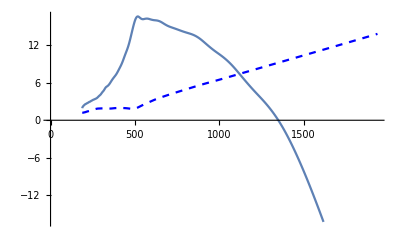

```mathematica
ListLinePlot[{Transpose[{lambdaInterpAu,orok}],Style[Transpose[{lambdaInterpAu,orok2}],Blue,Dashed]}]
```

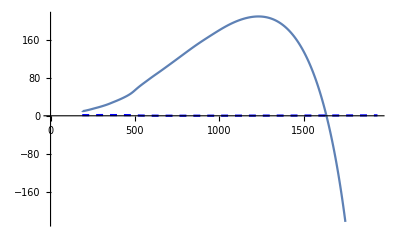

```mathematica
ListLinePlot[{Transpose[{lambdaInterpAu,oron}],Style[Transpose[{lambdaInterpAu,nInterpAu}],Blue,Dashed]}]
```

```mathematica
orobueno=selfconsrefractiveindex[omegaAu,nInterpAu,kInterpAu,50,1];
```

```mathematica
AbsoluteTiming[selfconsrefractiveindex[omegaAu,nInterpAu,kInterpAu,50,1]]
```

$Aborted

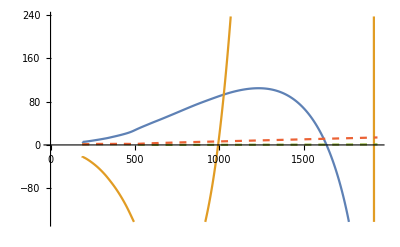

```mathematica
ListLinePlot[{Transpose[{lambdaInterpAu,orobueno[[1]]}],Style[Transpose[{lambdaInterpAu,orobueno[[2]]}]],Style[Transpose[{lambdaInterpAu,nInterpAu}],Dashed],Style[Transpose[{lambdaInterpAu,kInterpAu}],Dashed]}]
```

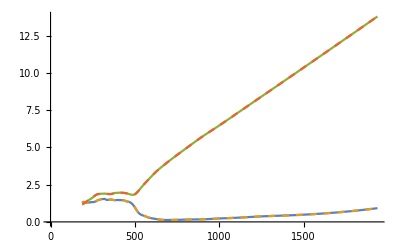

```mathematica
ListLinePlot[{Transpose[{lambdaInterpAu,orobueno[[1]]}],Style[Transpose[{lambdaInterpAu,nInterpAu}],Dashed],Transpose[{lambdaInterpAu,orobueno[[2]]}],Style[Transpose[{lambdaInterpAu,kInterpAu}],Dashed]}]
```